# Open XXZ chain

## 1. Model, conventions, and free parameters

```mathematica
ClearAll[XXZSpin, XXZHamiltonian, XXZCharges, XXZSplitCharge, XXZSectorED, XXZEdgeDensity, XXZRun, XXZValidate, XXZZeroQ];
Options[XXZHamiltonian] = {"UniformField" -> 0, "LeftField" -> 0,"RightField" -> 0};
XXZHamiltonian::params = "Use integer L>=3 and finite real J, Delta, h, bLeft, bRight.";
XXZSpin[l_Integer, a_Integer, j_Integer] :=
  KroneckerProduct @@ ReplacePart[
    ConstantArray[SparseArray[IdentityMatrix[2]], l],
    j -> SparseArray[PauliMatrix[a]/2]];
```

```mathematica
XXZHamiltonian[l_Integer, j_?NumericQ, delta_?NumericQ, OptionsPattern[]] :=
 Module[{h = OptionValue["UniformField"], bl = OptionValue["LeftField"],
   br = OptionValue["RightField"], sx, sy, sz},
  If[l < 3 || !And @@ (TrueQ[Element[#, Reals]] & /@ {j, delta, h, bl, br}),
    Message[XXZHamiltonian::params]; Return[$Failed]];
  sx = Table[XXZSpin[l, 1, k], {k, l}];
  sy = Table[XXZSpin[l, 2, k], {k, l}];
  sz = Table[XXZSpin[l, 3, k], {k, l}];
  SparseArray[j Sum[sx[[k]].sx[[k+1]] + sy[[k]].sy[[k+1]] +
      delta sz[[k]].sz[[k+1]], {k, l-1}] + h Total[sz] + bl First[sz] + br Last[sz]]
 ];
```

## 2. Symmetry operators and sector construction

```mathematica
XXZZeroQ[a_, tol_] := Max[Abs[Flatten[Normal[N[a]]]]] < tol;
```

```mathematica
XXZCharges[l_Integer, delta_] := Module[{d = 2^l, r, f, sx, sy, sz, s2,stagger, result},
  r = SparseArray[Table[{1+FromDigits[Reverse[IntegerDigits[k,2,l]],2], k+1}->1,
      {k,0,d-1}], {d,d}];
  f = SparseArray[Table[{d-k,k+1}->1,{k,0,d-1}],{d,d}];
  result = <|"R"->r, "F"->f, "RF"->r.f|>;
  If[TrueQ[delta == 1] || TrueQ[delta == -1],
    stagger = If[TrueQ[delta == -1], Table[(-1)^(k-1),{k,l}], ConstantArray[1,l]];
    sx = Total[Table[stagger[[k]]*XXZSpin[l,1,k],{k,l}]];
    sy = Total[Table[stagger[[k]]*XXZSpin[l,2,k],{k,l}]];
    sz = Total[Table[XXZSpin[l,3,k],{k,l}]];
    s2 = SparseArray[sx.sx + sy.sy + sz.sz];
    AssociateTo[result, If[TrueQ[delta == 1],"S2","StaggeredS2"] -> s2]];
  result
 ];
```

```mathematica
(* A sector basis is stored as columns in its magnetization subspace.
   Diagonalize each commuting charge within the already-resolved subspaces.
   Orthonormalize within equal-charge groups before further splitting. *)
XXZSplitCharge[sector_, q_, name_, tol_] := Module[{b = sector["Basis"],
    vals, vecs, groups, sub, label},
  {vals,vecs} = Eigensystem[N[ConjugateTranspose[b].q.b]];
  groups = Gather[Range[Length[vals]], Abs[vals[[#1]]-vals[[#2]]] < tol &];
  Table[
    sub = Transpose[Orthogonalize[vecs[[g]]]];
    label = If[MemberQ[{"S2","StaggeredS2"},name],
      Round[(-1+Sqrt[1+4 Re[Mean[vals[[g]]]]])/2,1/2],
      Round[Re[Mean[vals[[g]]]]]];
    <|"Basis"->b.sub, "Labels"->Append[sector["Labels"],
        If[name=="S2","S",If[name=="StaggeredS2","StaggeredS",name]]->label]|>,
    {g,groups}]
 ];
```

```mathematica
Options[XXZSectorED] = Join[Options[XXZHamiltonian], {"Tolerance"->10^-9}];
XXZSectorED::check = "A sector residual exceeded tolerance: `1`. No result returned.";
XXZSectorED[l_Integer, j_?NumericQ, delta_?NumericQ, OptionsPattern[]] :=
 Module[{h, charges, tol=OptionValue["Tolerance"], d=2^l, out={}, ids, hm,
    m, candidates, sectors, q, es, vals, rows, ord, b, fullRows, residual,
    leakage, active, pars, scale, eigTol, fields, eligible},
  pars = <|"L"->l,"J"->j,"Delta"->delta,
    "UniformField"->OptionValue["UniformField"],
    "LeftField"->OptionValue["LeftField"],"RightField"->OptionValue["RightField"]|>;
  h = XXZHamiltonian[l,j,delta,"UniformField"->pars["UniformField"],
    "LeftField"->pars["LeftField"],"RightField"->pars["RightField"]];
  If[h===$Failed,Return[$Failed]];
  scale = Max[1, Norm[h,Infinity]]; eigTol = 100 tol scale;
  charges = XXZCharges[l,delta];
  (* Enforce parameter conditions before numerical verification: a tiny
     nonzero field is not silently interpreted as an exact symmetry. *)
  fields = ConstantArray[pars["UniformField"],l];
  fields[[1]] += pars["LeftField"]; fields[[-1]] += pars["RightField"];
  eligible = Select[Keys[charges], Switch[#,
    "R", And@@MapThread[TrueQ[#1==#2]&,{fields,Reverse[fields]}],
    "F", And@@(TrueQ[#==0]& /@ fields),
    "RF", And@@MapThread[TrueQ[#1 == -#2]&,{fields,Reverse[fields]}],
    "S2"|"StaggeredS2", And@@(TrueQ[#==First[fields]]& /@ fields),
    _,False]&];
  active = Select[eligible, XXZZeroQ[h.charges[#]-charges[#].h,tol scale]&];
  Do[
    m = l/2-nDown;
    ids = Select[Range[d],Total[IntegerDigits[#-1,2,l]]==nDown&];
    hm = N[Normal[h[[ids,ids]]]];
    candidates = Select[active, !MemberQ[{"F","RF"},#] || m==0&];
    (* S^2 first, then spatial/discrete parities. *)
    candidates = SortBy[candidates, Switch[#,"S2"|"StaggeredS2",0,"R",1,"F",2,_,3]&];
    sectors = {<|"Basis"->IdentityMatrix[Length[ids]],"Labels"-><|"m"->m|>|>};
    Do[
      q = N[Normal[charges[name][[ids,ids]]]];
      sectors = Flatten[XXZSplitCharge[#,q,name,tol]& /@ sectors,1],
      {name,candidates}];
    Do[
      b = s["Basis"];
      leakage = Max[Abs[Flatten[hm.b-b.(ConjugateTranspose[b].hm.b)]]];
      {vals,rows} = Eigensystem[N[ConjugateTranspose[b].hm.b]];
      ord = Ordering[Re[vals]]; vals = Re[vals[[ord]]];
      (* Normalize/orthogonalize only within degenerate ENERGY eigenspaces. *)
      rows = rows[[ord]];
      Do[rows[[g]] = Orthogonalize[rows[[g]]],
        {g,Gather[Range[Length[vals]],Abs[vals[[#1]]-vals[[#2]]] < tol scale&]}];
      rows = Transpose[b.Transpose[rows]];
      residual = Max[MapThread[Norm[hm.#2-#1 #2]&,{vals,rows}]];
      If[Max[residual,leakage]>eigTol,
        Message[XXZSectorED::check,{s["Labels"],residual,leakage}];Return[$Failed]];
      fullRows = Table[Normal[SparseArray[Thread[ids->v],{d}]],{v,rows}];
      AppendTo[out,<|"Labels"->s["Labels"],"Dimension"->Length[vals],
        "BasisIndices"->ids,"SectorBasis"->b,"Eigenvalues"->Chop[vals],
        "Eigenvectors"->fullRows,"Residual"->residual,"Leakage"->leakage|>],
      {s,sectors}],
    {nDown,0,l}];
  <|"Parameters"->pars,"Hamiltonian"->h,"ActiveCharges"->active,
    "Sectors"->out,"Eigenvalues"->Sort[Flatten[Lookup[out,"Eigenvalues"]]],
    "DimensionSum"->Total[Lookup[out,"Dimension"]]|>
 ];
```

## 3. Edge reduced state: exact trace of the interior

```mathematica
(* Input is a normalized pure state in the usual site order {1,...,L}.
   Output order is {|up up>,|up down>,|down up>,|down down>} on {1,L}.
   The two edges need not be independent: their environment is shared. *)
XXZEdgeDensity[psi_List,l_Integer] := Module[{a},
  If[Length[psi]!=2^l,Return[$Failed]];
  a = ArrayReshape[Transpose[ArrayReshape[psi,{2,2^(l-2),2}],{1,3,2}],
    {4,2^(l-2)}];
  Chop[a.ConjugateTranspose[a]]
 ];
```

## 4. Spectrum

```mathematica
ClearAll[XXZSweepLabels,XXZPackSpectrum,XXZSameSpectrumQ,XXZSectorPanel];
(*----------Persistent sector labels----------*)
(*S is an additional label only at Delta=1. StaggeredS is an additional label only at Delta=-1. Remove these labels only when assembling the sweep plots.RF is redundant if both R and F are already specified.*)
XXZSweepLabels[labels_Association]:=Module[{a},a=KeyDrop[labels,{"S","StaggeredS"}];
If[KeyExistsQ[a,"R"]&&KeyExistsQ[a,"F"],a=KeyDrop[a,"RF"]];
KeySort[a]];
(*----------One panel for a sector or equivalent sectors----------*)
XXZSectorPanel[group_,results_,deltas_,parameterLabel_]:=Module[{styles,labels,energies,branches,curves={},lineStyles={}},styles=Table[Switch[k,1,Directive[Blue,AbsoluteThickness[2]],2,Directive[Orange,AbsoluteThickness[2],Dashed],_,Directive[ColorData[97][k],AbsoluteThickness[2],Dashing[{0.012,0.004,0.003,0.004}]]],{k,Length[group]}];
labels=Table[Row[KeyValueMap[Row[{#1,"=",#2,"  "}]&,First[results][key]["Labels"]]],{key,group}];
Do[energies=(#[group[[k]]]["Energies"]&/@results);
(*One curve for each energy ordered within this sector*)branches=(Transpose[{N[deltas],#}]&/@Transpose[energies]);
curves=Join[curves,branches];
lineStyles=Join[lineStyles,ConstantArray[styles[[k]],Length[branches]]],{k,Length[group]}];
ListLinePlot[Chop[curves],PlotStyle->lineStyles,InterpolationOrder->1,PlotRange->All,Frame->True,FrameLabel->{"Δ","Energy E"},PlotLabel->parameterLabel,LabelStyle->Directive[Black,13],ImageSize->700,PlotLegends->Placed[LineLegend[styles,labels],Below]]];
(*----------Diagonalize and organize one Delta----------*)
XXZPackSpectrum[l_,j_,delta_,h_,bl_,br_]:=Module[{result,groups},result=XXZSectorED[l,j,delta,"UniformField"->h,"LeftField"->bl,"RightField"->br];
If[!AssociationQ[result],Return[$Failed]];
groups=GatherBy[result["Sectors"],ToString[Normal[XXZSweepLabels[#["Labels"]]],InputForm]&];
Association[Table[ToString[Normal[XXZSweepLabels[First[group]["Labels"]]],InputForm]-><|"Labels"->XXZSweepLabels[First[group]["Labels"]],"Energies"->Sort[Flatten[Lookup[group,"Eigenvalues"]]]|>,{group,groups}]]];
(*----------Compare complete sector spectra----------*)
XXZSameSpectrumQ[keyA_,keyB_,results_,tolerance_]:=Module[{energiesA,energiesB,scale},energiesA=(#[keyA]["Energies"]&/@results);
energiesB=(#[keyB]["Energies"]&/@results);
If[Dimensions[energiesA]!=Dimensions[energiesB],Return[False]];
scale=Max[1,Max[Abs[Flatten[{energiesA,energiesB}]]]];
Max[Abs[Flatten[energiesA-energiesB]]]<tolerance scale];
```

```mathematica
(*----------Free parameters----------*)
spectrumL=6;
spectrumJ=1;                 (*Signed coupling*)
spectrumUniformField=0;
spectrumLeftField=0;
spectrumRightField=0;

spectrumDeltaList=Range[-5,5,0.01];
spectrumMatchingTolerance=10^-8;
```

```mathematica
(*----------Start parallel kernels----------*)
LaunchKernels[12];
DistributeDefinitions[XXZSpin,XXZHamiltonian,XXZCharges,XXZZeroQ,XXZSplitCharge,XXZSectorED,XXZSweepLabels,XXZPackSpectrum];
Print["Parallel kernels: ",Length[Kernels[]]];
```

```mathematica
(*Capture parameter values explicitly for the subkernels*)
{spectrumSeconds,spectrumResults}=AbsoluteTiming[With[{l=spectrumL,j=spectrumJ,h=spectrumUniformField,bl=spectrumLeftField,br=spectrumRightField},ParallelMap[XXZPackSpectrum[l,j,#,h,bl,br]&,spectrumDeltaList,Method->"CoarsestGrained"]]];
Print["Sweep time: ",spectrumSeconds," seconds."];
```

Sweep time: 1.58425 seconds.

Sectors: 14; separate panels: 9

Saved: C:\Users\Miguel\Documents\GitHub\Spin-transport\xxz_impurities_characterization\xxz_sector_spectra

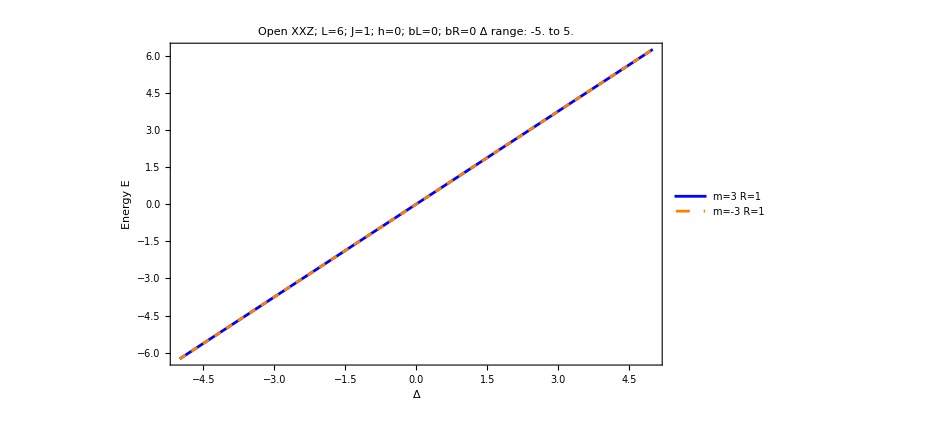
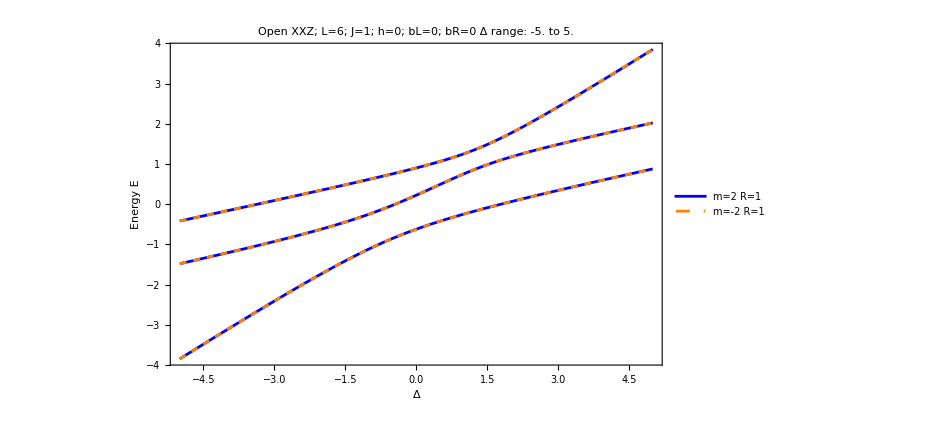
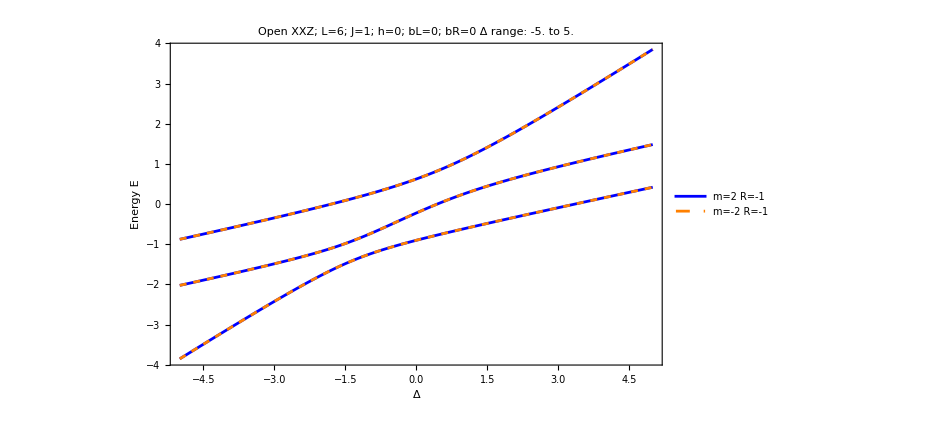
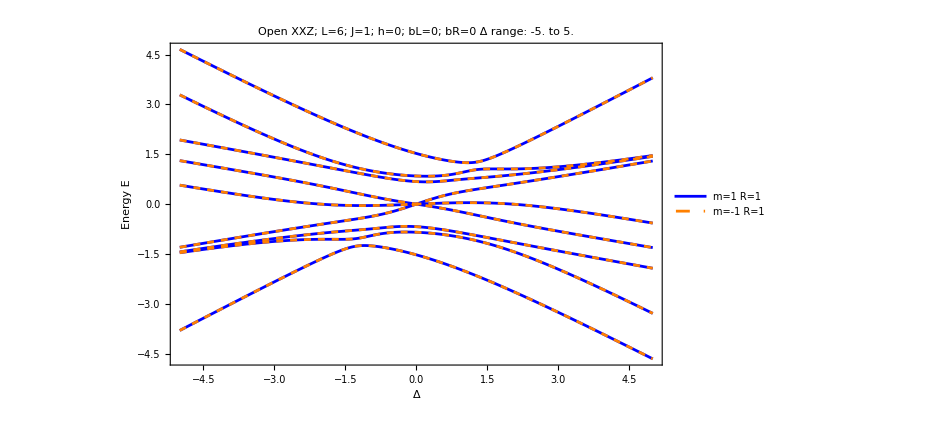
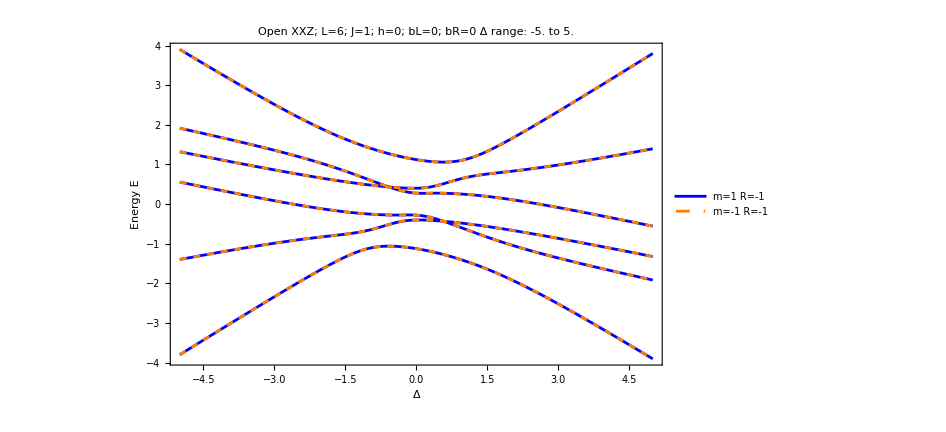
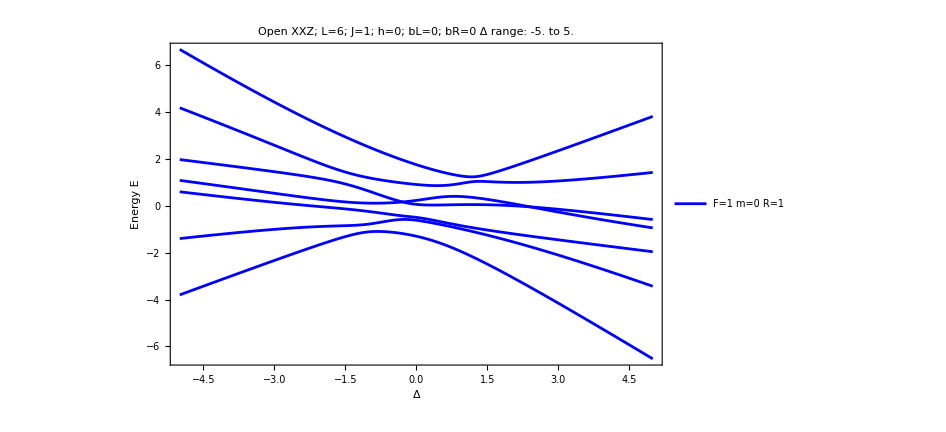
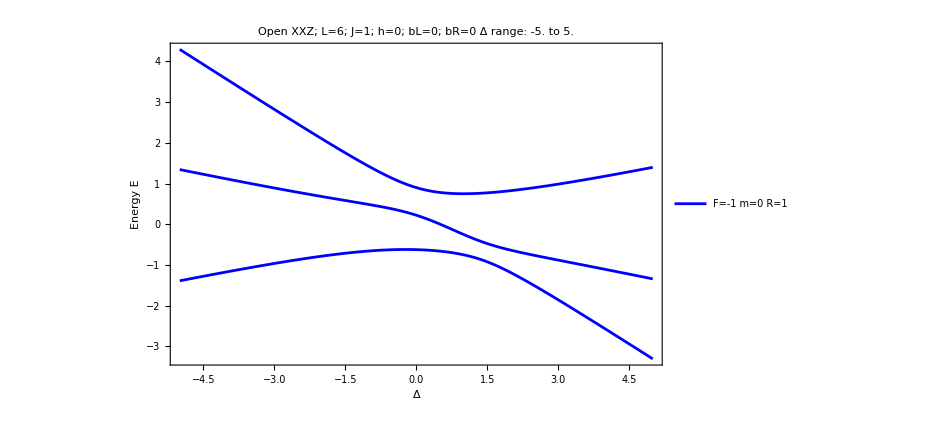
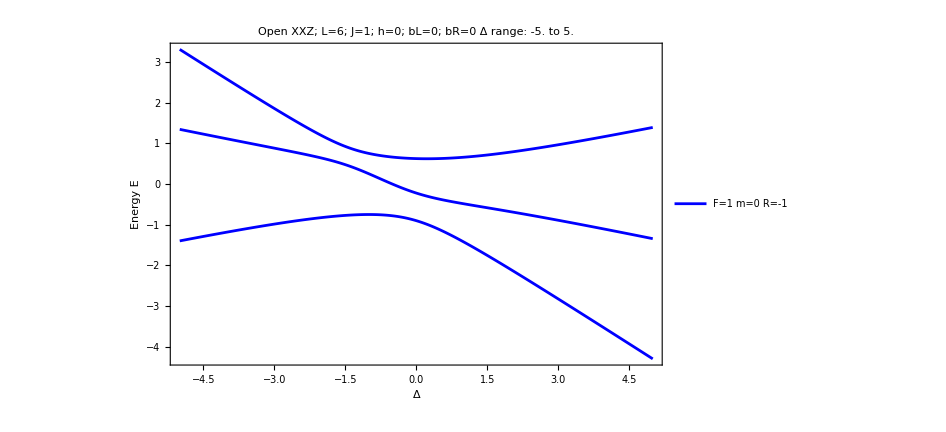

```mathematica
(*----------Check completeness,group,plot,and export----------*)
If[AllTrue[spectrumResults,AssociationQ],spectrumSectorKeys=Keys[First[spectrumResults]];
spectrumValidQ=AllTrue[spectrumResults,Sort[Keys[#]]==Sort[spectrumSectorKeys]&&Total[Length[#["Energies"]]&/@Values[#]]==2^spectrumL&];
If[spectrumValidQ,spectrumGroups=Gather[spectrumSectorKeys,XXZSameSpectrumQ[#1,#2,spectrumResults,spectrumMatchingTolerance]&];
spectrumParameterLabel=Row[{"Open XXZ; L=",spectrumL,"; J=",spectrumJ,"; h=",spectrumUniformField,"; bL=",spectrumLeftField,"; bR=",spectrumRightField,"\n","Δ range: ",First[spectrumDeltaList]," to ",Last[spectrumDeltaList]}];
spectrumPlots=XXZSectorPanel[#,spectrumResults,spectrumDeltaList,spectrumParameterLabel]&/@spectrumGroups;
(*Directory beside the notebook*)
spectrumDirectory=Quiet[Check[NotebookDirectory[],Directory[]]];
If[!StringQ[spectrumDirectory],spectrumDirectory=Directory[]];
spectrumOutputDirectory=FileNameJoin[{spectrumDirectory,"xxz_sector_spectra"}];
If[!DirectoryQ[spectrumOutputDirectory],CreateDirectory[spectrumOutputDirectory]];
Do[Export[FileNameJoin[{spectrumOutputDirectory,"sector_group_"<>ToString[k]<>".png"}],spectrumPlots[[k]]],{k,Length[spectrumPlots]}];
Print["Sectors: ",Length[spectrumSectorKeys],"; separate panels: ",Length[spectrumGroups]];
Print["Saved: ",spectrumOutputDirectory];
Column[spectrumPlots,Spacings->2],Print["Incomplete spectra or inconsistent sector labels."]],Print["A parallel diagonalization failed. Check spectrumResults."]]
```

# Reduced evolution